```mathematica
X0={10^-4,10^-4};
y={10^-5,10^-5};
c={1,1};
d={10^-6,10^-6};
kg={kg1,kg2};
a={10,10};
r={1,1,1};
max=0.01;
(*Parasets={c0,b31,b32,kg1,kg2,rp,a1}*)
kgsets=Table[i,{i,0,10,0.5}]
bsets=N[{1,10,25,50,100}/10]
C0=Table[i,{i,0.05,1,0.05}]
Parasets1=Flatten[Table[{kgsets[[i]],kgsets[[j]],C0[[k]]},{i,1,Length@kgsets},{j,1,Length@kgsets},{k,1,Length@C0}],2];
Length@Parasets1
Parasets2=Flatten[Table[{bsets[[i]],bsets[[j]]},{i,1,Length@bsets},{j,1,Length@bsets}],1]
Length@Parasets2
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.}

{0.1,1.,2.5,5.,10.}

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

8820

{{0.1,0.1},{0.1,1.},{0.1,2.5},{0.1,5.},{0.1,10.},{1.,0.1},{1.,1.},{1.,2.5},{1.,5.},{1.,10.},{2.5,0.1},{2.5,1.},{2.5,2.5},{2.5,5.},{2.5,10.},{5.,0.1},{5.,1.},{5.,2.5},{5.,5.},{5.,10.},{10.,0.1},{10.,1.},{10.,2.5},{10.,5.},{10.,10.}}

25

```mathematica
para={y1,y2,c1,c2,d1,d2,kg1,kg2,a1,a2,b31,b32,rs,ri,rp,p};
y1=y[[1]];
y2=y[[2]];
c1=c[[1]];
c2=c[[2]];
d1=d[[1]];
d2=d[[2]];
kg1=kg[[1]];
kg2=kg[[2]];
a1=a[[1]];
a2=a[[2]];
rs=r[[1]];
ri=r[[2]];
rp=r[[3]];
p=max;
```

```mathematica
Do[b=Parasets2[[k]];
b31=b[[1]];
b32=b[[2]];
index=1*b31/(Max@kgsets);
List1={};
List2={};
Do[c0=Parasets1[[i,3]];
c={1,c0};
c1=c[[1]];
c2=c[[2]];
kg={Parasets1[[i,1]],Parasets1[[i,2]]}*b31;
kg1=kg[[1]];
kg2=kg[[2]];
m1=((c1*d2*(kg1/b31)*y1)-(c2*d1*(kg2/b32)*y2))/(c2*d1*(kg2/b32)*y2);
m2=(kg1/b31)/rp;
var={iin1,iin2,iout,pin1,pin2,pout,x1,x2};
eqn1={iin1'[t]==a1-ri*(iin1[t]-iout[t]),
iin2'[t]==-a2*iin2[t]+ri*(iout[t]-iin2[t]),
pin1'[t]==-((kg1*pin1[t])/(b31+pin1[t]))+rp*(pout[t]-pin1[t]),
pin2'[t]==a2*iin2[t]-((kg2*pin2[t])/(b32+pin2[t]))+rp*(pout[t]-pin2[t]),
iout'[t]==x1[t]*ri*(iin1[t]-iout[t])-x2[t]*ri*(iout[t]-iin2[t]),
pout'[t]==x2[t]*rp*(pin2[t]-pout[t])-x1[t]*rp*(pout[t]-pin1[t]),
x1'[t]==(((kg1*pin1[t])/(b31+pin1[t]))*c1*y1*x1[t]*(1-((x1[t]+x2[t])/p)))-d1*x1[t],
x2'[t]==(((kg2*pin2[t])/(b32+pin2[t]))*c2*y2*x2[t]*(1-((x1[t]+x2[t])/p)))-d2*x2[t]
};
eqn2={iin1[0]==0,
iin2[0]==0,
iout[0]==0,
pin1[0]==0,
pin2[0]==0,
pout[0]==0,
x1[0]==X0[[1]],
x2[0]==X0[[2]]};
eqn=Join[eqn1,eqn2];
result=NDSolve[eqn,var,{t,0,100000000},Method->{"EquationSimplification"->"Residual"}];
iin1v=Flatten@Evaluate[iin1[90000000]/.result];
iin2v=Flatten@Evaluate[iin2[90000000]/.result];
pin1v=Flatten@Evaluate[pin1[90000000]/.result];
pin2v=Flatten@Evaluate[pin2[90000000]/.result];
ioutv=Flatten@Evaluate[iout[90000000]/.result];
poutv=Flatten@Evaluate[pout[90000000]/.result];
x1b=Flatten@Evaluate[{x1[90000000]}/.result];
x2b=Flatten@Evaluate[{x2[90000000]}/.result];
biomass=x1b+x2b;
x1ratio=Flatten@Evaluate[{x1[90000000]/(x1[90000000]+x2[90000000])}/.result];
x2ratio=Flatten@Evaluate[{x2[90000000]/(x1[90000000]+x2[90000000])}/.result];
List1=Join[List1,{{First@iin1v,First@iin2v,First@pin1v,First@pin2v,First@ioutv,First@poutv,First@x1b,First@x2b,First@biomass,First@x1ratio,First@x2ratio}}];
List2=Join[List2,{{m1,m2,First@x2ratio,First@biomass,First@pin1v,First@pin2v}}];
If[Divisible[i,8000]==True,Print[k]];
,{i,1,Length@Parasets1}];
Export[FileNameJoin[{NotebookDirectory[],"Data","b="<>ToString@Parasets2[[k]]<>".xlsx"}],List1];
Export[FileNameJoin[{NotebookDirectory[],"Data","plot-b="<>ToString@Parasets2[[k]]<>".xlsx"}],List2];
,{k,1,25}];
```

```mathematica
Listplot=Table[{List2[[m,1]],List2[[m,2]],If[List2[[m,4]]<0.0001,-10,100*List2[[m,3]]]},{m,Length@List2}];
desplot=ListDensityPlot[Listplot,ColorFunction->"BlueGreenYellow",PlotRange->{{0,10},{0,10},{-1,100}},PlotLegends->Automatic,LabelStyle->Directive[Black,Bold,36],Frame->True,FrameStyle->Directive[Thickness[0.005],Black,Bold,30],InterpolationOrder->1.0,Mesh->None]
ListPointPlot3D@Listplot
```

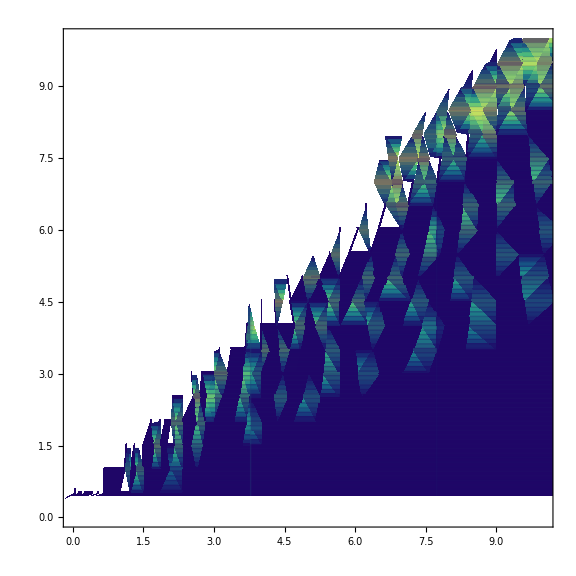

```mathematica
Gridplot={};
Do[
List2=Flatten[Import[FileNameJoin[{NotebookDirectory[],"Data","plot-b="<>ToString@Parasets2[[k]]<>".xlsx"}]],1];
Listplot=Table[{List2[[m,1]],List2[[m,2]],If[List2[[m,4]]<0.0001,-10,100*List2[[m,3]]]},{m,Length@List2}];
desplot=ListDensityPlot[Listplot,ColorFunction->"BlueGreenYellow",PlotRange->{{0,10},{0,10},{-1,100}},LabelStyle->Directive[Black,Bold,60],Frame->True,FrameStyle->Directive[Thickness[0.006],Black,Bold,60],ImageSize->Large,InterpolationOrder->1.0,Mesh->100];
Gridplot=Join[Gridplot,{desplot}];
,{k,1,25}];
Gridplot1=GraphicsGrid[Partition[Gridplot,5],ImageSize->5000];
Export[FileNameJoin[{NotebookDirectory[],"gridplot1.tif"}],Gridplot1];
desplot
```